# Resolution functions

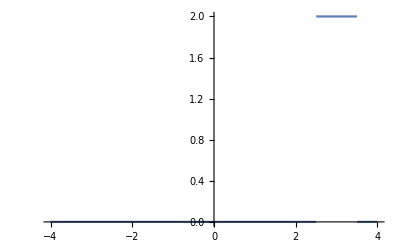

```mathematica
R[z_,c_,w_,h_]:=h UnitStep[(w/2)^2-(z-c)^2];
Plot[R[z,3,1,2],{z,-4,4}]
```

## Rectangle

```mathematica
K[z_,zm_,Δm_]:=If[z>=(zm-Δm/2)&&z<=(zm+Δm/2),1/Δm,0];
```

### Convolution with a rectangle

```mathematica
MyMin[x_,y_]:=If[x<=y,x,y];
MyMax[x_,y_]:=If[x≥y,x,y];
Overlap[min1_,max1_,min2_,max2_]:=MyMax[0,MyMin[max1,max2]-MyMax[min1,min2]];

KConv[z_,zm_,Δm_,c_,w_,h_]:=h/Δm Overlap[zm-Δm/2,zm+Δm/2,c-w/2,c+w/2];

FullSimplify[(Integrate[K[z,zm,Δm]R[z,c,w,h],{z,-∞,∞}]==KConv[z,zm,Δm,c,w,h])/.{Δm->1},Assumptions->{h>0,w>0}]
```

True

## Lorentzian

1

0.5

0.5

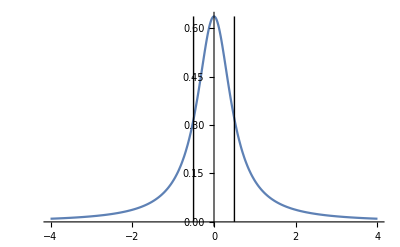

```mathematica
L[z_,zm_,Δm_]:=1/π(Δm/2)/((z-zm)^2+(Δm/2)^2);
Integrate[L[z,zm,Δm],{z,-∞,∞},Assumptions->{Δm>0,zm∈Reals}]

(* Δm is the width at half-height *)
N[L[zm-Δm/2,zm,Δm]/L[zm,zm,Δm]]
N[L[zm+Δm/2,zm,Δm]/L[zm,zm,Δm]]

zm=0;
Δm=1;
Plot[{L[z,zm,Δm]},{z,-4,4},
Epilog->{Line[{{zm-Δm/2,0},{zm-Δm/2,L[zm,zm,Δm]}}],Line[{{zm+Δm/2,0},{zm+Δm/2,L[zm,zm,Δm]}}]}]
Unset[{zm,Δm}];
```

### Convolution with a rectangle

```mathematica
LConv[z_,zm_,Δm_,c_,w_,h_]:=h(ArcTan[(c+w/2-zm)/(Δm/2)]-ArcTan[(c-w/2- zm)/(Δm/2)])/π

FullSimplify[
Integrate[L[z,zm,Δm]R[z,c,w,h],{z,-∞,∞},Assumptions->{w>0,Δm>0,zm∈Reals,c∈Reals}]==LConv[z,zm,Δm,c,w,h],Assumptions->{w>0,Δm>0,zm∈Reals,c∈Reals}
]
```

True

## Gaussian

1

0.606531

0.606531

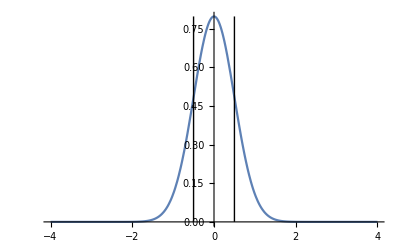

```mathematica
G[z_,zm_,Δm_]:=1/Sqrt[2π (Δm/2)^2] Exp[-(z-zm)^2/(2(Δm/2)^2)];
Integrate[G[z,zm,Δm],{z,-∞,∞},Assumptions->{Δm>0,zm∈Reals}]

(* Δm is approximately the width at half-height *)
N[G[zm-Δm/2,zm,Δm]/G[zm,zm,Δm]]
N[G[zm+Δm/2,zm,Δm]/G[zm,zm,Δm]]

zm=0;
Δm=1;
Plot[{G[z,zm,Δm]},{z,-4,4},
Epilog->{Line[{{zm-Δm/2,0},{zm-Δm/2,G[zm,zm,Δm]}}],Line[{{zm+Δm/2,0},{zm+Δm/2,G[zm,zm,Δm]}}]}]
Unset[{zm,Δm}];
```

### Convolution with a rectangle

```mathematica
GConv[z_,zm_,Δm_,c_,w_,h_]:=h/2 (Erf[((c+w/2)-zm)/(√2 (Δm/2))]-Erf[((c-w/2)-zm)/(√2(Δm/2))]);

FullSimplify[Integrate[G[z,zm,Δm]R[z,c,w,h],{z,c-w/2,c+w/2},Assumptions->{w>0,Δm>0,zm∈Reals,c∈Reals}]==GConv[z,zm,Δm,c,w,h],Assumptions->{w>0,Δm>0,zm∈Reals,c∈Reals}]
```

True

## Unit tests

```mathematica
configurations0={
R[z,0,1,2]+R[z,1,4,1]+R[z,3,2,3],
R[z,-0.1,1,2]+R[z,0.9,4,1]+R[z,2.9,2,3],
R[z,-0.2,1,2]+R[z,0.8,4,1]+R[z,2.8,2,3]
};
configurations1={
R[z,0,1,2]+R[z,-1,4,1]+R[z,-3,2,3],
R[z,0.1,1,2]+R[z,-0.9,4,1]+R[z,-2.9,2,3],
R[z,0.2,1,2]+R[z,-0.8,4,1]+R[z,-2.8,2,3]
};

zmΔmmesh={{-5.0,2.5},{-2.5,2.5},{0.0,2.5},{2.5,2.5},{5.0,2.5}};
zmΔmintervals={{-4.0,2.0},{0.0,2.0},{4.0,2.0}};

MyNF[x_]:=NumberForm[x,11,ScientificNotationThreshold->{-10,10}];
```

```mathematica
avgr[conf_,zm_,Δm_]:=Module[{J=Length[conf]},1/J Sum[NIntegrate[K[z,zm,Δm]conf[[j]],{z,-∞,∞}],{j,1,J}]];
avgl[conf_,zm_,Δm_]:=Module[{J=Length[conf]},1/J Sum[NIntegrate[L[z,zm,Δm]conf[[j]],{z,-∞,∞}],{j,1,J}]];
avgg[conf_,zm_,Δm_]:=Module[{J=Length[conf]},1/J Sum[NIntegrate[G[z,zm,Δm]conf[[j]],{z,-∞,∞}],{j,1,J}]];
```

```mathematica
(* spectral_integrals() *)
conf[z_]:=R[z,0,1,2]+R[z,1,4,1]+R[z,3,2,3];

MyNF[NIntegrate[K[z,2.0,1.5]conf[z],{z,-∞,∞}]]
MyNF[NIntegrate[L[z,2.0,1.5]conf[z],{z,-∞,∞}]]
MyNF[NIntegrate[G[z,2.0,1.5]conf[z],{z,-∞,∞}]]

MyNF[Map[NIntegrate[K[z,#1[[1]],#1[[2]]]conf[z],{z,-∞,∞}]&,zmΔmmesh]]
MyNF[Map[NIntegrate[L[z,#1[[1]],#1[[2]]]conf[z],{z,-∞,∞}]&,zmΔmmesh]]
MyNF[Map[NIntegrate[G[z,#1[[1]],#1[[2]]]conf[z],{z,-∞,∞}]&,zmΔmmesh]]

MyNF[Map[NIntegrate[K[z,#1[[1]],#1[[2]]]conf[z],{z,-∞,∞}]&,zmΔmintervals]]
MyNF[Map[NIntegrate[L[z,#1[[1]],#1[[2]]]conf[z],{z,-∞,∞}]&,zmΔmintervals]]
MyNF[Map[NIntegrate[G[z,#1[[1]],#1[[2]]]conf[z],{z,-∞,∞}]&,zmΔmintervals]]
```

2.5

1.9842074284

2.4419081106

{0.,0.,1.7,2.8,0.3}

{0.11425323448,0.33160051874,1.317775872,1.8161452063,0.62132091407}

{0.00099456210459,0.20874479607,1.5639704932,2.367126337,0.66607947844}

{0.,2.,1.5}

{0.13416633572,1.4467315501,1.2823782799}

{0.0018083638019,1.6740000753,1.5908630342}

```mathematica
(* spectral_avg_mesh() *)
MyNF[Map[avgr[configurations0,#1[[1]],#1[[2]]]&,zmΔmmesh]]
MyNF[Map[avgr[configurations1,#1[[1]],#1[[2]]]&,zmΔmmesh]]

MyNF[Map[avgl[configurations0,#1[[1]],#1[[2]]]&,zmΔmmesh]]
MyNF[Map[avgl[configurations1,#1[[1]],#1[[2]]]&,zmΔmmesh]]

MyNF[Map[avgg[configurations0,#1[[1]],#1[[2]]]&,zmΔmmesh]]
MyNF[Map[avgg[configurations1,#1[[1]],#1[[2]]]&,zmΔmmesh]]
```

{0.,0.,1.74,2.88,0.18}

{0.18,2.88,1.74,0.,0.}

{0.11813549348,0.35165088927,1.3401479841,1.8189434995,0.5816390449}

{0.5816390449,1.8189434995,1.3401479841,0.35165088927,0.11813549348}

{0.0013523815169,0.24123931979,1.6095326791,2.3600231333,0.59687177639}

{0.59687177639,2.3600231333,1.6095326791,0.24123931979,0.0013523815169}

```mathematica
{"0.59687177639","2.3600231333","1.6095326791","0.24123931979","0.0013523815169"}
```

{0.596872,2.36002,1.60953,0.241239,0.00135238}

```mathematica
(* spectral_avg_intervals() *)
MyNF[Map[avgr[configurations0,#1[[1]],#[[2]]]&,zmΔmintervals]]
MyNF[Map[avgr[configurations1,#1[[1]],#[[2]]]&,zmΔmintervals]]

MyNF[Map[avgl[configurations0,#1[[1]],#[[2]]]&,zmΔmintervals]]
MyNF[Map[avgl[configurations1,#1[[1]],#[[2]]]&,zmΔmintervals]]

MyNF[Map[avgg[configurations0,#1[[1]],#[[2]]]&,zmΔmintervals]]
MyNF[Map[avgg[configurations1,#1[[1]],#[[2]]]&,zmΔmintervals]]
```

{0.,2.,1.35}

{1.35,2.,0.}

{0.13993900613,1.4659822436,1.1905339934}

{1.1905339934,1.4659822436,0.13993900613}

{0.0026140415807,1.7088851639,1.4631864139}

{1.4631864139,1.7088851639,0.0026140415807}

```mathematica
dispr[conf_,zm_,Δm_]:=Module[{J=Length[conf]},1/J Sum[(NIntegrate[K[z,zm,Δm]conf[[j]],{z,-∞,∞}]-avgr[conf,zm,Δm])^2,{j,1,J}]];
displ[conf_,zm_,Δm_]:=Module[{J=Length[conf]},1/J Sum[(NIntegrate[L[z,zm,Δm]conf[[j]],{z,-∞,∞}]-avgl[conf,zm,Δm])^2,{j,1,J}]];
dispg[conf_,zm_,Δm_]:=Module[{J=Length[conf]},1/J Sum[(NIntegrate[G[z,zm,Δm]conf[[j]],{z,-∞,∞}]-avgg[conf,zm,Δm])^2,{j,1,J}]];
```

```mathematica
(* spectral_disp_mesh() *)
MyNF[Map[dispr[configurations0,#1[[1]],#[[2]]]&,zmΔmmesh]]
MyNF[Map[dispr[configurations1,#1[[1]],#[[2]]]&,zmΔmmesh]]

MyNF[Map[displ[configurations0,#1[[1]],#[[2]]]&,zmΔmmesh]]
MyNF[Map[displ[configurations1,#1[[1]],#[[2]]]&,zmΔmmesh]]

MyNF[Map[dispg[configurations0,#1[[1]],#[[2]]]&,zmΔmmesh]]
MyNF[Map[dispg[configurations1,#1[[1]],#[[2]]]&,zmΔmmesh]]
```

{0.,0.,0.0010666666667,0.0042666666667,0.0096}

{0.0096,0.0042666666667,0.0010666666667,0.,0.}

{0.000010223050954,0.00027568188841,0.00031187673322,0.0000045914585024,0.0010213267979}

{0.0010213267979,0.0000045914585024,0.00031187673322,0.00027568188841,0.000010223050954}

{0.000000093709688562,0.00072794781645,0.0013622646134,0.000048934828621,0.0031216266776}

{0.0031216266776,0.000048934828621,0.0013622646134,0.00072794781645,0.000000093709688562}

```mathematica
(* spectral_disp_intervals() *)
MyNF[Map[dispr[configurations0,#1[[1]],#[[2]]]&,zmΔmintervals]]
MyNF[Map[dispr[configurations1,#1[[1]],#[[2]]]&,zmΔmintervals]]

MyNF[Map[displ[configurations0,#1[[1]],#[[2]]]&,zmΔmintervals]]
MyNF[Map[displ[configurations1,#1[[1]],#[[2]]]&,zmΔmintervals]]

MyNF[Map[dispg[configurations0,#1[[1]],#[[2]]]&,zmΔmintervals]]
MyNF[Map[dispg[configurations1,#1[[1]],#[[2]]]&,zmΔmintervals]]
```

{0.,0.,0.015}

{0.015,0.,0.}

{0.000022713760152,0.00021728508944,0.0055832956437}

{0.0055832956437,0.00021728508944,0.000022713760152}

{0.00000048333940716,0.00076900174659,0.010843485563}

{0.010843485563,0.00076900174659,0.00000048333940716}

```mathematica
corrr[conf_,zm1_,Δm1_,zm2_,Δm2_]:=Module[{J=Length[conf]},1/J Sum[
(NIntegrate[K[z,zm1,Δm1]conf[[j]],{z,-∞,∞}]-avgr[conf,zm1,Δm1])(NIntegrate[K[z,zm2,Δm2]conf[[j]],{z,-∞,∞}]-avgr[conf,zm2,Δm2]),
{j,1,J}]];
corrl[conf_,zm1_,Δm1_,zm2_,Δm2_]:=Module[{J=Length[conf]},1/J Sum[
(NIntegrate[L[z,zm1,Δm1]conf[[j]],{z,-∞,∞}]-avgl[conf,zm1,Δm1])(NIntegrate[L[z,zm2,Δm2]conf[[j]],{z,-∞,∞}]-avgl[conf,zm2,Δm2]),
{j,1,J}]];
corrg[conf_,zm1_,Δm1_,zm2_,Δm2_]:=Module[{J=Length[conf]},1/J Sum[
(NIntegrate[G[z,zm1,Δm1]conf[[j]],{z,-∞,∞}]-avgg[conf,zm1,Δm1])(NIntegrate[G[z,zm2,Δm2]conf[[j]],{z,-∞,∞}]-avgg[conf,zm2,Δm2]),
{j,1,J}]];
```

```mathematica
(* spectral_corr_mesh() *)
MyNF[Table[corrr[configurations0,zmΔmmesh[[m1]][[1]],zmΔmmesh[[m1]][[2]],zmΔmmesh[[m2]][[1]],zmΔmmesh[[m2]][[2]]],
{m1,1,Length[zmΔmmesh]},{m2,1,Length[zmΔmmesh]}]]
MyNF[Table[corrr[configurations1,zmΔmmesh[[m1]][[1]],zmΔmmesh[[m2]][[2]],zmΔmmesh[[m2]][[1]],zmΔmmesh[[m2]][[2]]],
{m1,1,Length[zmΔmmesh]},{m2,1,Length[zmΔmmesh]}]]

MyNF[Table[corrl[configurations0,zmΔmmesh[[m1]][[1]],zmΔmmesh[[m1]][[2]],zmΔmmesh[[m2]][[1]],zmΔmmesh[[m2]][[2]]],
{m1,1,Length[zmΔmmesh]},{m2,1,Length[zmΔmmesh]}]]
MyNF[Table[corrl[configurations1,zmΔmmesh[[m1]][[1]],zmΔmmesh[[m2]][[2]],zmΔmmesh[[m2]][[1]],zmΔmmesh[[m2]][[2]]],
{m1,1,Length[zmΔmmesh]},{m2,1,Length[zmΔmmesh]}]]

MyNF[Table[corrg[configurations0,zmΔmmesh[[m1]][[1]],zmΔmmesh[[m1]][[2]],zmΔmmesh[[m2]][[1]],zmΔmmesh[[m2]][[2]]],
{m1,1,Length[zmΔmmesh]},{m2,1,Length[zmΔmmesh]}]]
MyNF[Table[corrg[configurations1,zmΔmmesh[[m1]][[1]],zmΔmmesh[[m2]][[2]],zmΔmmesh[[m2]][[1]],zmΔmmesh[[m2]][[2]]],
{m1,1,Length[zmΔmmesh]},{m2,1,Length[zmΔmmesh]}]]
```

{{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.0010666666667,0.0021333333333,-0.0032},{0.,0.,0.0021333333333,0.0042666666667,-0.0064},{0.,0.,-0.0032,-0.0064,0.0096}}

{{0.0096,-0.0064,-0.0032,0.,0.},{-0.0064,0.0042666666667,0.0021333333333,0.,0.},{-0.0032,0.0021333333333,0.0010666666667,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.}}

{{0.000010223050954,0.000053085574758,0.00005629498948,0.0000040838502197,-0.00010210316023},{0.000053085574758,0.00027568188841,0.00029211848579,0.000020947305001,-0.00053000597741},{0.00005629498948,0.00029211848579,0.00031187673322,0.000024846607216,-0.00056396445954},{0.0000040838502197,0.000020947305001,0.000024846607216,0.0000045914585024,-0.000042941398753},{-0.00010210316023,-0.00053000597741,-0.00056396445954,-0.000042941398753,0.0010213267979}}

{{0.0010213267979,-0.000042941398753,-0.00056396445954,-0.00053000597741,-0.00010210316023},{-0.000042941398753,0.0000045914585024,0.000024846607216,0.000020947305001,0.0000040838502197},{-0.00056396445954,0.000024846607216,0.00031187673322,0.00029211848579,0.00005629498948},{-0.00053000597741,0.000020947305001,0.00029211848579,0.00027568188841,0.000053085574758},{-0.00010210316023,0.0000040838502197,0.00005629498948,0.000053085574758,0.000010223050954}}

{{0.000000093709688562,0.0000082504869412,0.000011254655116,-0.0000021098304105,-0.000017027314249},{0.0000082504869412,0.00072794781645,0.00099494075555,-0.0001842656817,-0.0015056905602},{0.000011254655116,0.00099494075555,0.0013622646134,-0.00024950226612,-0.0020621151724},{-0.0000021098304105,-0.0001842656817,-0.00024950226612,0.000048934828621,0.00037706007634},{-0.000017027314249,-0.0015056905602,-0.0020621151724,0.00037706007634,0.0031216266776}}

{{0.0031216266776,0.00037706007634,-0.0020621151724,-0.0015056905602,-0.000017027314249},{0.00037706007634,0.000048934828621,-0.00024950226612,-0.0001842656817,-0.0000021098304105},{-0.0020621151724,-0.00024950226612,0.0013622646134,0.00099494075555,0.000011254655116},{-0.0015056905602,-0.0001842656817,0.00099494075555,0.00072794781645,0.0000082504869412},{-0.000017027314249,-0.0000021098304105,0.000011254655116,0.0000082504869412,0.000000093709688562}}

```mathematica
(* spectral_corr_intervals() *)
MyNF[Table[corrr[configurations0,zmΔmintervals[[m1]][[1]],zmΔmintervals[[m1]][[2]],zmΔmintervals[[m2]][[1]],zmΔmintervals[[m2]][[2]]],
{m1,1,Length[zmΔmintervals]},{m2,1,Length[zmΔmintervals]}]]
MyNF[Table[corrr[configurations1,zmΔmintervals[[m1]][[1]],zmΔmintervals[[m2]][[2]],zmΔmintervals[[m2]][[1]],zmΔmintervals[[m2]][[2]]],
{m1,1,Length[zmΔmintervals]},{m2,1,Length[zmΔmintervals]}]]

MyNF[Table[corrl[configurations0,zmΔmintervals[[m1]][[1]],zmΔmintervals[[m1]][[2]],zmΔmintervals[[m2]][[1]],zmΔmintervals[[m2]][[2]]],
{m1,1,Length[zmΔmintervals]},{m2,1,Length[zmΔmintervals]}]]
MyNF[Table[corrl[configurations1,zmΔmintervals[[m1]][[1]],zmΔmintervals[[m2]][[2]],zmΔmintervals[[m2]][[1]],zmΔmintervals[[m2]][[2]]],
{m1,1,Length[zmΔmintervals]},{m2,1,Length[zmΔmintervals]}]]

MyNF[Table[corrg[configurations0,zmΔmintervals[[m1]][[1]],zmΔmintervals[[m1]][[2]],zmΔmintervals[[m2]][[1]],zmΔmintervals[[m2]][[2]]],
{m1,1,Length[zmΔmintervals]},{m2,1,Length[zmΔmintervals]}]]
MyNF[Table[corrg[configurations1,zmΔmintervals[[m1]][[1]],zmΔmintervals[[m2]][[2]],zmΔmintervals[[m2]][[1]],zmΔmintervals[[m2]][[2]]],
{m1,1,Length[zmΔmintervals]},{m2,1,Length[zmΔmintervals]}]]
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.015}}

{{0.015,0.,0.},{0.,0.,0.},{0.,0.,0.}}

{{0.000022713760152,0.000069478090619,-0.00035600284583},{0.000069478090619,0.00021728508944,-0.0010930462744},{-0.00035600284583,-0.0010930462744,0.0055832956437}}

{{0.0055832956437,-0.0010930462744,-0.00035600284583},{-0.0010930462744,0.00021728508944,0.000069478090619},{-0.00035600284583,0.000069478090619,0.000022713760152}}

{{0.00000048333940716,0.000019101542105,-0.000072110868004},{0.000019101542105,0.00076900174659,-0.0028844581059},{-0.000072110868004,-0.0028844581059,0.010843485563}}

{{0.010843485563,-0.0028844581059,-0.000072110868004},{-0.0028844581059,0.00076900174659,0.000019101542105},{-0.000072110868004,0.000019101542105,0.00000048333940716}}